```mathematica
Limit[Sin[n x]/x,x->0]
```

n

```mathematica
F[w_]:=∫_-n^n ⅇ^(-I w t)ⅆt
n=2
```

2

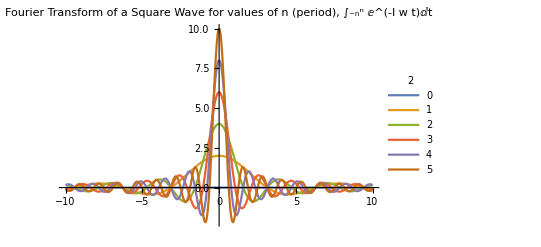

```mathematica
Plot[Evaluate@Table[∫_-n^n ⅇ^(-I w t)ⅆt,{n,0,5}],{w,-10,10},PlotLabel->"Fourier Transform of a Square Wave for values of n (period), ∫_-n^n ⅇ^(-I w t)ⅆt",PlotLegends->LineLegend[Table[n,{n,0,5}],LegendLabel->n],PlotRange->All]
```